Articles for comparison:
R&I: https://arxiv.org/pdf/1202.2841.pdf
Dolgov et. al: https://arxiv.org/pdf/hep-ph/9703315.pdf
Mangano et. al: https://arxiv.org/pdf/hep-ph/0506164.pdf
Hannestad&Madsen: https://arxiv.org/pdf/astro-ph/9506015.pdf

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/pyBBN/tests/sbbn_oscillations

```mathematica
FileToNumLevel2[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {2}]
];
```

```mathematica
FileToNumLevel1[lines_]:=Module[{func, var, buf},
func = Function[x, var=StringToStream@x;buf=Read[var,Number];Close@var;buf];
Map[func, lines, {1}]
];
```

#### Elecrton neutrinos

```mathematica
rawlinesEl = Import["./output/Electron_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesEl = StringSplit/@rawlinesEl[[2;;]];
linesEl = FileToNumLevel2[linesEl];
```

```mathematica
T= Last[linesEl][[2]];
distEl1=Last[linesEl][[3;;]];
yEl=FileToNumLevel1[StringSplit[rawlinesEl[[1]]][[4;;]]];
plotDataEl=Transpose[{yEl, distEl1}];
```

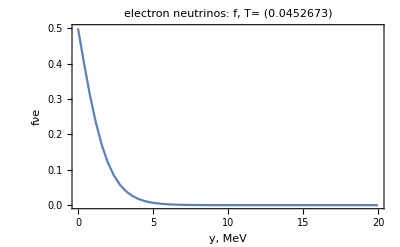

```mathematica
ListLinePlot[plotDataEl,PlotLabel->Style[#,Bold,15]&/@{"electron neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνe"},PlotRange->All]
```

#### Muon neutrinos

```mathematica
rawlinesμ = Import["./output/Muon_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesμ = StringSplit/@rawlinesμ[[2;;]];
linesμ=FileToNumLevel2[linesμ];
```

```mathematica
Tμ= Last[linesμ][[2]];
distμ=Last[linesμ][[3;;]];
yμ=FileToNumLevel1[StringSplit[rawlinesμ[[1]]][[4;;]]];
plotDataμ=Transpose[{yμ, distμ}];
```

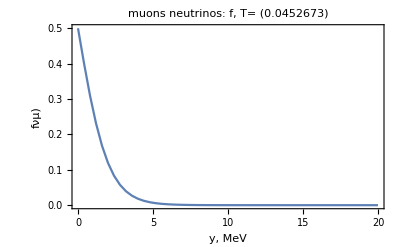

```mathematica
ListLinePlot[plotDataμ,PlotLabel->Style[#,Bold,15]&/@{"muons neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fνμ)"},PlotRange->All]
```

#### Tau neutrinos

```mathematica
rawlinesτ = Import["./output/Tau_neutrino.distribution.txt", {"Text", "Lines"}][[2;; ]];
```

```mathematica
linesτ = StringSplit/@rawlinesτ[[2;;]];
linesτ=FileToNumLevel2[linesτ];
```

```mathematica
Tτ= Last[linesτ][[2]];
distτ=Last[linesτ][[3;;]];
yτ=FileToNumLevel1[StringSplit[rawlinesτ[[1]]][[4;;]]];
plotDataτ=Transpose[{yτ, distτ}];
```

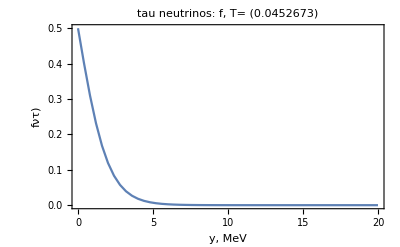

```mathematica
ListLinePlot[plotDataτ,PlotLabel->Style[#,Bold,15]&/@{"tau neutrinos: f, T= "@T},Frame-> True, FrameLabel->{"y, MeV","fντ)"},PlotRange->All]
```

## Final spectrum. Comparison with previous results (Fig. 10)

```mathematica
(*final-spectra-SM.eps*)
multiplier={#⟦1⟧,#⟦2⟧*(Exp[#⟦1⟧]+1)}&;
(*finalspectraSMTest2015Electron =multiplier/@Import["../tests/standard_model_bbn/spectrum_Electron neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015ElectronFunc = Interpolation[finalspectraSMTest2015Electron];
finalspectraSMTest2015Muon = multiplier/@Import["../tests/standard_model_bbn/spectrum_Muon neutrino.dat","HeaderLines"->1];
finalspectraSMTest2015MuonFunc = Interpolation[finalspectraSMTest2015Muon];*)
```

```mathematica
plotfEl=Interpolation[multiplier/@plotDataEl];
plotfμ=Interpolation[multiplier/@plotDataμ];
plotfτ=Interpolation[multiplier/@plotDataτ];
```

```mathematica
finalspectraSMth13zeroTest=Import["../../figures/Figures-sources/Final-spectra-SM/oscillations+SM-th13=0.dat","HeaderLines"->3];
finalspectranueSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-nue-th13=0.tsv"];
finalspectranumuSMDigit=Import["../../figures/Figures-sources/Final-spectra-SM/Mangano-numu-th13=0.tsv"];
finalnueSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,4}]]];
finalnumuSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,8}]]];
finalnutauSMth13zeroTestFunc=Interpolation[finalspectraSMth13zeroTest[[All,{1,12}]]];
finalspectranueSMth13zeroDigitFunc=Interpolation[finalspectranueSMDigit[[All,{1,2}]]];
finalspectranumuSMth13zeroDigitFunc=Interpolation[finalspectranumuSMDigit[[All,{1,2}]]];
"To get from the basis of nu_mu and nu_tau we used (with theta_23=0) to the physical basis, used by Mangano, we take an average of the distributions";
```

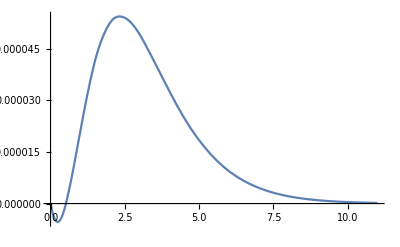

```mathematica
Plot[finalnumuSMth13zeroTestFunc[y]-finalnutauSMth13zeroTestFunc[y],{y,0,11}]
```

InterpolatingFunction::dmval: Input value {0.000224714} lies outside the range of data in the interpolating function. Extrapolation will be used.

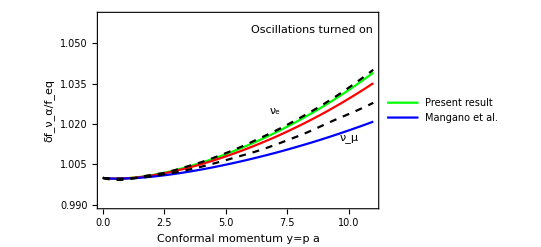

```mathematica
Plot[{plotfEl[y],
plotfμ[y],plotfτ[y],finalspectranueSMth13zeroDigitFunc[y],finalspectranumuSMth13zeroDigitFunc[y]},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y=p a","δf_ν_α/f_eq"},PlotStyle->{{Green},{Red},{Blue},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.025}],Text["ν_μ",{10,1.015}],Text["Oscillations turned on",{8.5,1.055}]},
PlotLegends->{"Present result",None,"Mangano et al.",None}]
Export["final-spectra-SM-oscill-separate.eps",%];
```

InterpolatingFunction::dmval: Input value {0.000224714} lies outside the range of data in the interpolating function. Extrapolation will be used.

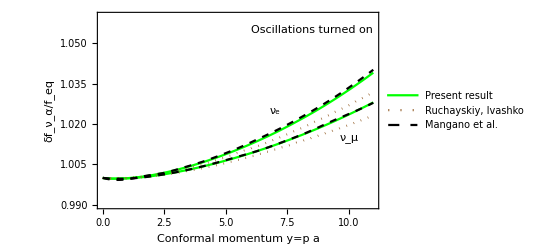

```mathematica
Plot[{plotfEl[y],
0.5(plotfμ[y]+plotfτ[y]),finalnueSMth13zeroTestFunc[y]*(Exp[y]+1),0.5(finalnumuSMth13zeroTestFunc[y]+finalnutauSMth13zeroTestFunc[y])*(Exp[y]+1),finalspectranueSMth13zeroDigitFunc[y],finalspectranumuSMth13zeroDigitFunc[y]},{y,0,11},PlotRange->{{0,11},{0.99,1.06}},Frame->True,FrameLabel->{"Conformal momentum y=p a","δf_ν_α/f_eq"},PlotStyle->{{Green},{Green},{Brown, Dotted},{Brown, Dotted},{Black,Dashed},{Black,Dashed}},Epilog->{Text["ν_e",{7,1.025}],Text["ν_μ",{10,1.015}],Text["Oscillations turned on",{8.5,1.055}]},
PlotLegends->{"Present result",None,"Ruchayskiy, Ivashko",None,"Mangano et al.",None}]
Export["final-spectra-SM-oscill.eps",%];
```

## Evolution of spectrum

```mathematica
aEllist=First[Transpose[linesEl]];
setofdistributionsEl=Transpose[Transpose[linesEl][[3 ;;]]];
setofdistributionsEl1=Transpose[{yEl,#}]&/@setofdistributionsEl;
interpolatedDistEl=Interpolation/@setofdistributionsEl1;
```

```mathematica
aμlist=First[Transpose[linesμ]];
setofdistributionsμ=Transpose[Transpose[linesμ][[3 ;;]]];
setofdistributionsμ1=Transpose[{yμ,#}]&/@setofdistributionsμ;
interpolatedDistμ=Interpolation/@setofdistributionsμ1;
```

```mathematica
aτlist=First[Transpose[linesτ]];
setofdistributionsτ=Transpose[Transpose[linesτ][[3 ;;]]];
setofdistributionsτ1=Transpose[{yτ,#}]&/@setofdistributionsτ;
interpolatedDistτ=Interpolation/@setofdistributionsτ1;
```

### Comparison with Fig 1 of Mangano’s paper

```mathematica
f10El=Interpolation[Transpose[{0.5*aEllist,#[10]&/@interpolatedDistEl}]];
f10μ=Interpolation[Transpose[{0.5*aμlist,#[10]&/@interpolatedDistμ}]];
f10τ=Interpolation[Transpose[{0.5*aτlist,#[10]&/@interpolatedDistτ}]];
```

```mathematica
f10El[0.1]*(Exp[10]+1)-1
```

0.000918909

```mathematica
f10μ[0.1]*(Exp[10]+1)-1
```

0.000886512

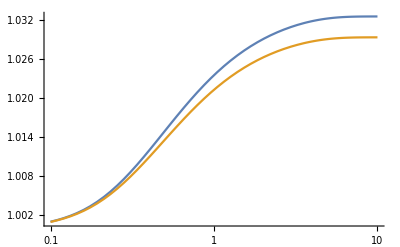

```mathematica
LogLinearPlot[{f10El[x]*(Exp[10]+1),f10μ[x]*(Exp[10]+1)},{x,0.1,10},Ticks -> Automatic]
```

```mathematica
deltafnue10Mangano=Import["../../figures/Figures-sources/sm-deltafnue_comp/mangano_dfn-nue-osc13=0_y10.dat","HeaderLines"->1];
deltafnue10ManganoFunc=Interpolation[deltafnue10Mangano[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
deltafnuμ10Mangano=Import["../../figures/Figures-sources/sm-deltafnumu_comp/mangano_dfn-numu-osc13=0_y10.dat","HeaderLines"->1];
deltafnuμ10ManganoFunc=Interpolation[deltafnuμ10Mangano[[All,{1,2}]],InterpolationOrder->2,Method->"Spline"];
```

```mathematica
(deltafnuμ10ManganoFunc[10]-f10μ[10]*(Exp[10]+1))/(f10μ[10]*(Exp[10]+1))
```

-0.00541198

InterpolatingFunction::dmval: Input value {0.0500064} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

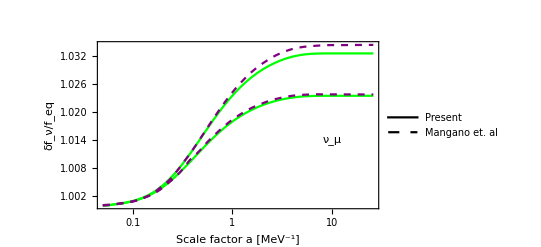

```mathematica
Show[LogLinearPlot[{f10El[x]*(Exp[10]+1),0.5(f10μ[x]+f10τ[x])*(Exp[10]+1),deltafnue10ManganoFunc[x],deltafnuμ10ManganoFunc[x]},{x,0.05,26},PlotRange->All(*{{0.1,7},{0,0.025}}*),Frame->True,FrameLabel->{"Scale factor a [MeV^-1]","δf_ν/f_eq"},PlotStyle->{{Green},{Green},{Purple, Dashed},{Purple, Dashed}},Epilog->{Text["Standard Model BBN",{Log[0.1],1.04}],Text["ν_e",{Log[10],1.041}],Text["ν_μ",{Log[10],1.014}]},PlotLegends->LineLegend[{Thick,Dashed},{"Present","Mangano et. al"}]]]
Export["final-spectra-SM-10-oscill.eps",%];
```